```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*
ΓMathematica[[i, j, k]] = Γ^i_{k j}

*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
Γ'[r][[1,1,1]]//FullSimplify
```

(-((-1+z'[r]^2) z''[r]^2)+z'[r] (1+z'[r]^2) z^(3)[r])/((1+z'[r]^2)^2)

```mathematica
(*\Nabla_r v^r*)
```

```mathematica
Δv[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
ig[r]
```

{{1/(1+z'[r]^2),0},{0,1/r^2}}

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
Cross[e[1][{r,θ}],e[2][{r,θ}]].Cross[e[1][{r,θ}],e[2][{r,θ}]]//FullSimplify
```

r^2 (1+z'[r]^2)

```mathematica
n[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
n[{r,θ}]
```

{-(Cos[θ] z'[r])/(√(1+z'[r]^2)),-(Sin[θ] z'[r])/(√(1+z'[r]^2)),1/(√(1+z'[r]^2))}

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].n[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].n[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].n[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].n[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] D[(r^2 H'[r])/sqrtdetg[r],r]
```

```mathematica
b[r]//MatrixForm
```

(z''[r]/(√(1+z'[r]^2)) | 0
0 | (r z'[r])/(√(1+z'[r]^2)))

```mathematica
eqs=FullSimplify[{   
Δv[r]==0,
0==σ'[r]+η 2 (D[Δv[r],r]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] 
},Assumptions->ass]
```

{v'[r] (1+z'[r]^2)+v[r] z'[r] z''[r]==0,σ'[r]+2 η (v''[r]+(z''[r] (v'[r] (z'[r]+z'[r]^3)-v[r] (-1+z'[r]^2) z''[r])+v[r] z'[r] (1+z'[r]^2) z^(3)[r])/((1+z'[r]^2)^2))==0,1/(2 (1+z'[r]^2)^(9/2))((z'[r] (1+z'[r]^2)^3)/r^3+(z'[r] (1+z'[r]^2)^4)/r^3-(2 σ[r] z'[r] (1+z'[r]^2)^4)/r-(3 (1+z'[r]^2)^2 z''[r])/r^2+((1+z'[r]^2)^3 z''[r])/r^2-2 σ[r] (1+z'[r]^2)^3 z''[r]+2 v[r]^2 (1+z'[r]^2)^4 z''[r]-(15 z'[r] (1+z'[r]^2) z''[r]^2)/r-35 z''[r]^3+30 (1+z'[r]^2) z''[r]^3+(4 (1+z'[r]^2)^2 z^(3)[r])/r-20 z'[r] (1+z'[r]^2) z''[r] z^(3)[r]+2 (1+z'[r]^2)^2 z^(4)[r])==0}

```mathematica
κ=1;
η=1;
ρ=1;
Rmin=1;
Rmax=2;
```

```mathematica
bcs={
v[Rmin]==2,v'[Rmin]==-1,
σ[Rmin]==37/16,
z'[Rmin]==1,z''[Rmin]==1,z'''[Rmin]==1,z''''[Rmin]==-1
};
```

```mathematica
repbcs={
v[Rmin]->2,v'[Rmin]->-1,
σ[Rmin]->37/16,
z'[Rmin]->1,z''[Rmin]->1,z'''[Rmin]->1,z''''[Rmin]->-1
};
```

```mathematica
(eqs)/.{r->Rmin}/.repbcs//FullSimplify
```

{True,1+σ'[1]+2 v''[1]==0,True}

```mathematica
s=NDSolve[Flatten[{eqs,bcs}],{v,σ,z},{r,Rmin,Rmax}]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

{{v→InterpolatingFunction[…],σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

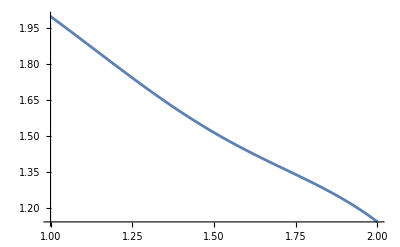

```mathematica
Plot[Evaluate[v[r]/. s],{r,Rmin,Rmax},PlotRange->All]
```

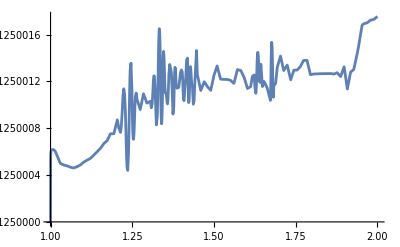

```mathematica
Plot[Evaluate[σ[r]/. s],{r,Rmin,Rmax},PlotRange->All]
```

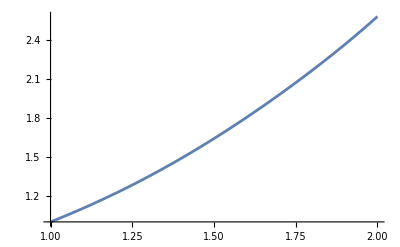

```mathematica
Plot[Evaluate[z[r]/. s],{r,Rmin,Rmax},PlotRange->All]
```

```mathematica
(σ'[r]+η 2 (D[Δv[r],r]))/.s/.{r->1.9}
```

{-0.0714662}